```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3, 1/2<x≤3/2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
C2r=Simplify[h[x],3/2<x≤5/2]/.x->3/2
C3l=Simplify[h[x],3/2<x≤5/2]/.x->5/2
```

1+c01/2+c02/4+c03/8

1/2 (-c11+1/2 (c12-c13/2))

1/2 (c11+1/2 (c12+c13/2))

1/2 (-c21+1/2 (c22-c23/2))

1/2 (c21+1/2 (c22+c23/2))

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 (c12+c22),c03}

{0,-2 c11-4 c21,0,-2 (c13+2 c23)}

```mathematica
(*Smoothness*)
S0=Simplify[D[h[x],x],0<x<1/2]/.x->0
S1l=Simplify[D[h[x],x],0<x<1/2]/.x->1/2
S1r=Simplify[D[h[x],x],1/2<x<3/2]/.x->1/2
S2l=Simplify[D[h[x],x],1/2<x<3/2]/.x->3/2
S2r=Simplify[D[h[x],x],3/2<x<5/2]/.x->3/2
S3l=Simplify[D[h[x],x],3/2<x<5/2]/.x->5/2
```

c01

c01+1/2 (2 c02+(3 c03)/2)

c11+1/2 (-2 c12+(3 c13)/2)

c11+1/2 (2 c12+(3 c13)/2)

c21+1/2 (-2 c22+(3 c23)/2)

c21+1/2 (2 c22+(3 c23)/2)

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==C2r,
	C3l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T1[[2]]==1,
	T1[[4]]==0,
	S0==0,
	S1l==S1r,
	S2l==S2r,
	S3l==0
	},
	{c01,c02,c03,c11,c12,c13,c21,c22,c23}
]
```

{{c01→0,c02→-7/4,c03→0,c11→-9/16,c12→1,c13→-1/4,c21→1/32,c22→-1/8,c23→1/8}}

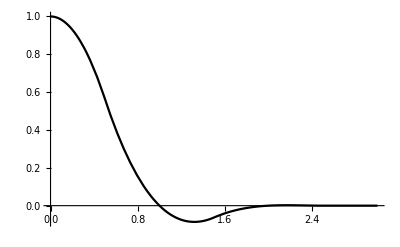

```mathematica
Plot[h[x]/.GenSols[[1]],{x,0,3},PlotStyle->Black]
```

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
SumF1=SumF1/.φ->1/2;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

(-32 (-16+59 y-68 y^2+12 y^3)-4 x^3 (-96+101 y+140 y^2+52 y^3)+4 x^2 (544+315 y-1476 y^2+140 y^3)-x (-1888+957 y+1260 y^2+404 y^3))/4096
(x (689-1097 y+512 y^2-60 y^3)-4 x^3 (-51+131 y-64 y^2+4 y^3)+4 (-5+41 y-56 y^2+20 y^3)-4 x^2 (-281+523 y-298 y^2+52 y^3))/1024
1/512 (-179+377 y-296 y^2+80 y^3+8 x^3 (-10+17 y-10 y^2+2 y^3)+4 x^2 (-74+133 y-87 y^2+20 y^3)+x (-377+731 y-532 y^2+136 y^3))
-((1+x) (-2+y) (-901+476 y-52 y^2+12 x (-39+4 y+4 y^2)+4 x^2 (11-36 y+12 y^2)))/8192
-((2+x) (5+2 x)^2 (5-2 y)^2 (-2+y))/8192
0

(-864-1989 y+5548 y^2-436 y^3-16 x^2 (208-3 y-474 y^2+4 y^3)+4 x^3 (96+101 y-140 y^2+52 y^3)-x (-7392+351 y+14748 y^2+92 y^3))/4096
(-973-3549 y-1736 y^2-204 y^3+4 x^3 (51+131 y+64 y^2+4 y^3)-8 x^2 (217+458 y+245 y^2+32 y^3)+x (3549+6853 y+3664 y^2+524 y^3))/1024
1/512 (-8 x^3 (10+17 y+10 y^2+2 y^3)+4 x^2 (134+235 y+147 y^2+32 y^3)+4 (361+444 y+314 y^2+78 y^3)-x (1209+2203 y+1468 y^2+344 y^3))
(13492+4170 y+584 y^2-88 y^3+4 x^3 (22+83 y+60 y^2+12 y^3)-4 x^2 (-146+191 y+252 y^2+60 y^3)+x (-4170-1885 y+764 y^2+332 y^3))/8192
(842-9555 y-4116 y^2-588 y^3+133 x (2+y) (5+2 y)^2-40 x^2 (2+y) (5+2 y)^2+4 x^3 (2+y) (5+2 y)^2)/8192
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5}=Parallelize[{
	Simplify[D[SumF1a1,{{x,y}}]],
	Simplify[D[SumF1a2,{{x,y}}]],
	Simplify[D[SumF1a3,{{x,y}}]],
Simplify[D[SumF1a4,{{x,y}}]],
Simplify[D[SumF1a5,{{x,y}}]],
	Simplify[D[SumF1b1,{{x,y}}]],
	Simplify[D[SumF1b2,{{x,y}}]],
	Simplify[D[SumF1b3,{{x,y}}]],
Simplify[D[SumF1b4,{{x,y}}]],
Simplify[D[SumF1b5,{{x,y}}]]
}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1b1,Err1b2,Err1b3,Err1b4,Err1b5}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-2-1/2)^(-1-1/2) (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(3-1/2)^(4-1/2) (DSumF1b5.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5]
N[Err1]
```

94211027/660602880

0.142614